(0.00127717 (0.365148-√(1-0.0106996 r^2)))/(-1.09545+√(1-0.0106996 r^2))

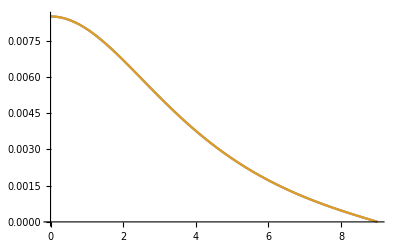

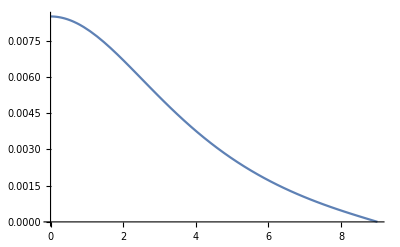

```mathematica
R:=9
M:=3.9
ρ0:=3M/(4 π R^3)
m[r]:=4/3 π r^3 ρ0
my0=1*10^(-9);
pc:=ρ0*(1-(1-2M/R)^(1/2))/(3*(1-2M/R)^(1/2)-1)
eqnP:={-p'[r]==(ρ0+p[r])*(m[r]+4*π*r^3*p[r])/(r^2*(1-2*m[r]/r))}
condP:={p[my0]==pc}
systemP:=Join[eqnP,condP]
state=First[NDSolve`ProcessEquations[systemP, {p}, {r, my0, R}]];
NDSolve`Iterate[state,R]
sol=NDSolve`ProcessSolutions[state];
pexakt[r]=ρ0((1-2M/R)^(1/2)-(1-2M r^2/(R^3))^(1/2))/((1-2 M r^2 /R^3)^(1/2)-3(1-2 M/R)^(1/2))
(*sol=NDSolve[systemP,p,{r,my0,R}]*)
Plot[{Evaluate[p[r]/.sol],Evaluate[pexakt[r]]},{r,my0,R}]
Plot[Evaluate[pexakt[r]],{r,my0,R}]
```